```mathematica
p:=ContourPlot[{x^2+y^2/4==5/16,x^2+y^2/4==9/25*5/16,x^2+y^2/4==(9/25)^2*5/16,x^2+y^2/4==(9/25)^3*5/16,x^2+y^2/4==(9/25)^4*5/16,x^2+y^2/4==(9/25)^5*5/16},{x,-0.7,0.7},{y,-1.2,1.3},AspectRatio->25/14]
```

```mathematica
a2:=VectorPlot[{-2*x,-y/2},{x,-0.7,0.7},{y,-1.2,1.3},AspectRatio->25/14, Frame->False];
a4:=Graphics[{Thick,Blue,Arrow[{{1/4,1},{-11/20,1/5}}], 
Text[Style["(x,y)", Large], {2/5,1.1}],
Text[Style["s", Large], {-12/20,1/5}],
Text[Style["Gradient Descent: learning rate"  , Medium, Background -> LightRed], {0,1.3}]}];
a5:=Graphics[{Thick,Blue,Arrow[{{1/4,1},{-11/20,1/5}}], 
Text[Style["(x,y)", Large], {2/5,1.1}],
Text[Style["s", Large], {-12/20,1/5}],
Text[Style["Gradient Descent: learning rate"  , Medium, Background -> LightRed], {0,1.3}]}];
a6:=Graphics[{Arrow[{{1/4,1},{(-3/5)/4,(3/5)}}],
Text[Style["Gradient Descent: learning rate"  , Medium, Background -> LightRed], {0,1.3}]}];
```

```mathematica
b3=ParametricPlot[{Exp[-2*t]/4,Exp[-t/2]},{t,-4*Log[10/7],20},Frame->False, PlotStyle->Red,AspectRatio->1/4];
b4:=ListPlot[{{1/4,1}}, PlotStyle -> {Black, PointSize[Large]}, Axes -> None];
b5:=ListPlot[{{1/4,1}}, PlotStyle -> {Black, PointSize[Large]}, Axes -> None];
b7:=Graphics[{Arrow[{{(-3/5)/4,(3/5)},{(-3/5)^2/4,(3/5)^2}}]}];
```

```mathematica
c5:=ListPlot[{{(-3/5)/4,(3/5)}}, PlotStyle -> {Red, PointSize[Large]}, Axes -> None];
c8:=Graphics[{Arrow[{{(-3/5)^2/4,(3/5)^2},{(-3/5)^3/4,(3/5)^3}}]}];
```

```mathematica
d9:=Graphics[{Arrow[{{(-3/5)^3/4,(3/5)^3},{(-3/5)^4/4,(3/5)^4}}]}];
```

```mathematica
e10:=Graphics[{Arrow[{{(-3/5)^4/4,(3/5)^4},{(-3/5)^5/4,(3/5)^5}}]}]
```

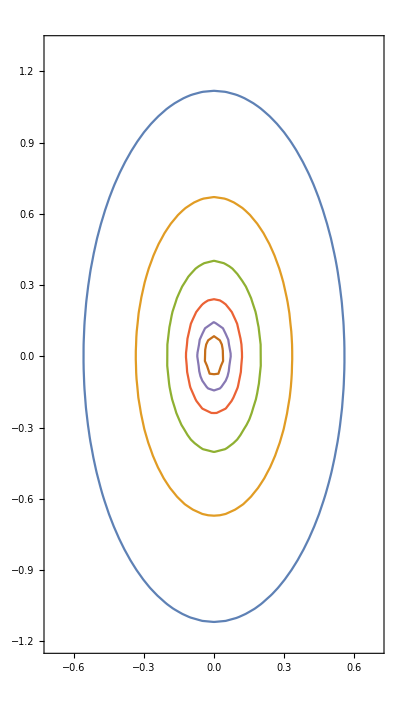

```mathematica
Show[p]
```

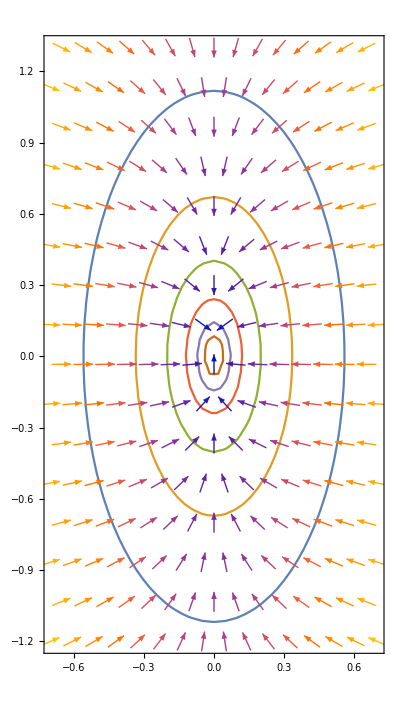

```mathematica
Show[p,a2]
```

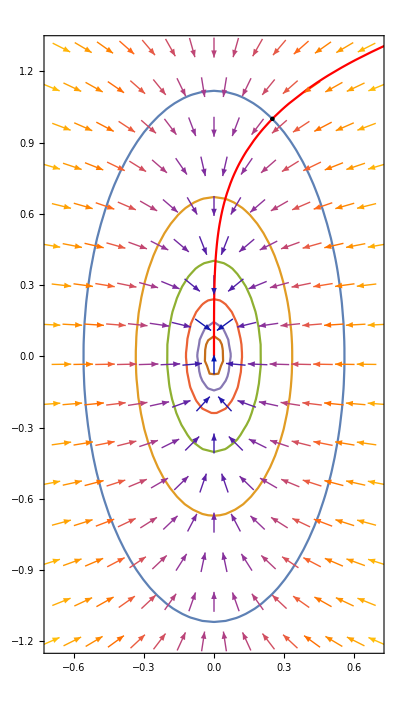

```mathematica
Show[p,a2,b3,b4]
```

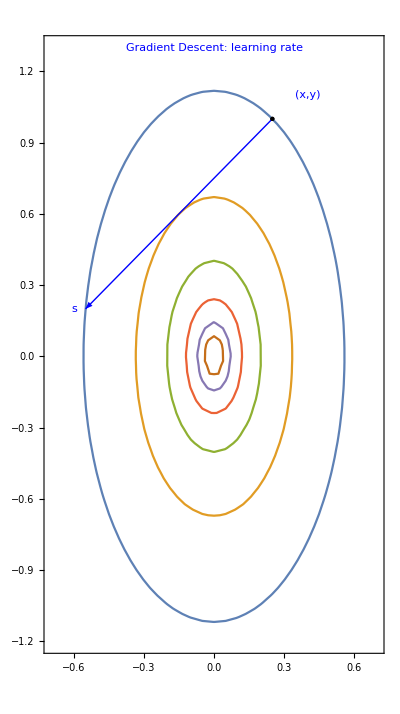

```mathematica
Show[p,a4,b4]
```

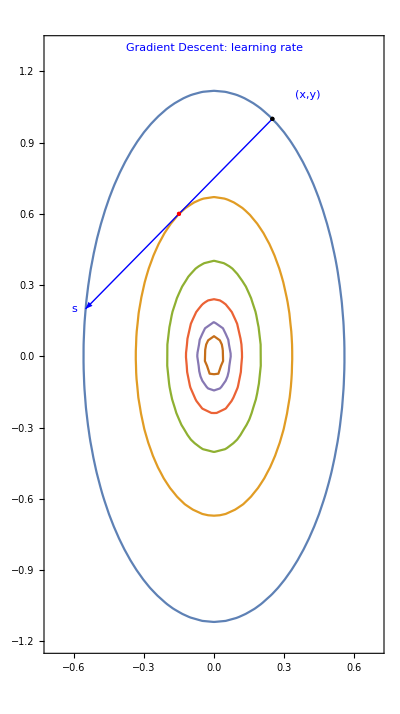

```mathematica
Show[p,a5,b5,c5]
```

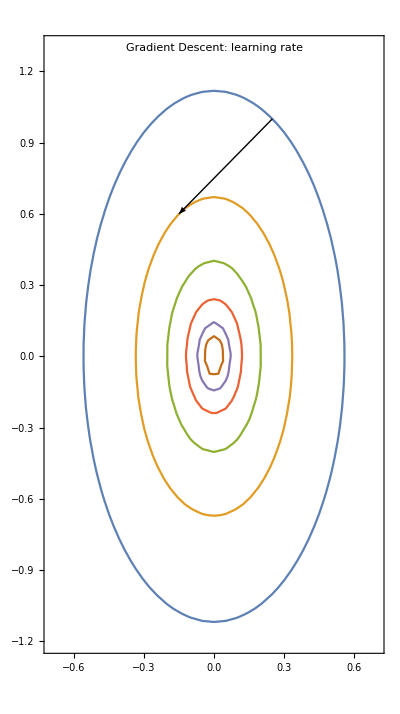

```mathematica
Show[p,a6]
```

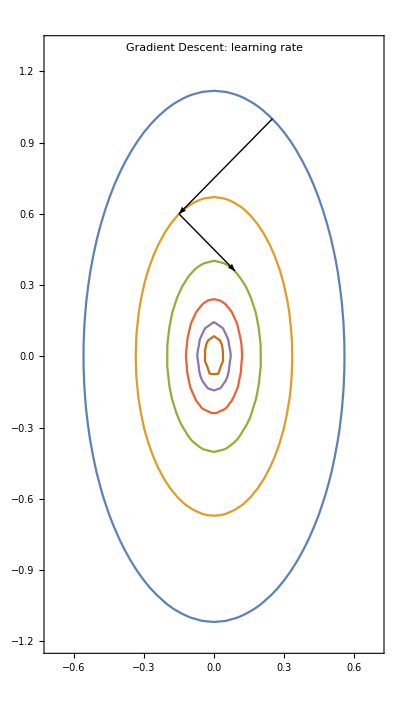

```mathematica
Show[p,a6,b7]
```

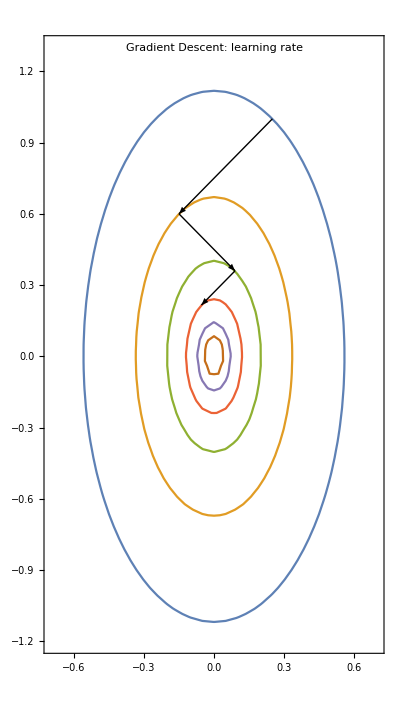

```mathematica
Show[p,a6,b7,c8]
```

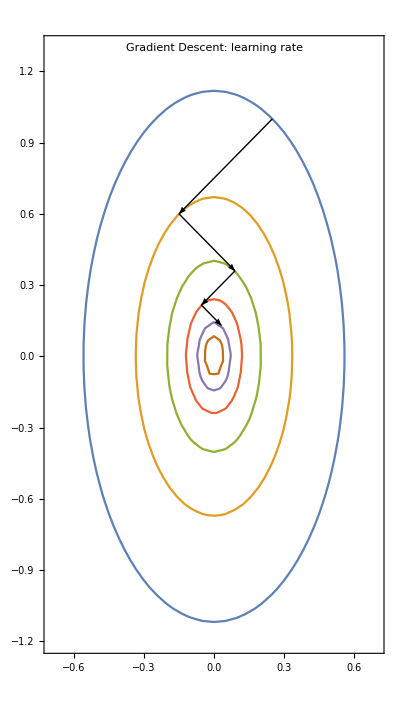

```mathematica
Show[p,a6,b7,c8,d9]
```

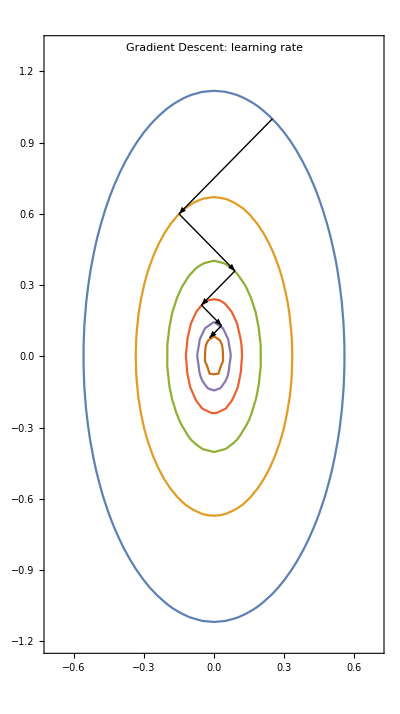

```mathematica
Show[p,a6,b7,c8,d9,e10]
```